```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Graphics"],FontFamily->"Flama Light",FontSize->11]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
file90=FileNames["MSD-MT-suc90-"<>"*.csv"]
```

{MSD-MT-suc90-00.csv,MSD-MT-suc90-01.csv,MSD-MT-suc90-02.csv,MSD-MT-suc90-03.csv,MSD-MT-suc90-04.csv,MSD-MT-suc90-05.csv,MSD-MT-suc90-06.csv,MSD-MT-suc90-07.csv,MSD-MT-suc90-08.csv}

```mathematica
data90=Table[Import[file90[[i]],"Data"][[2;;-1]],{i,Length[file90]}];
```

```mathematica
yaxis=Import[file90[[1]],"Data"][[1]]
```

{lag time [sec],MSD-longitudinal [um^2],MSD-transversal [um^2],MSAD-transversal [rad^2]}

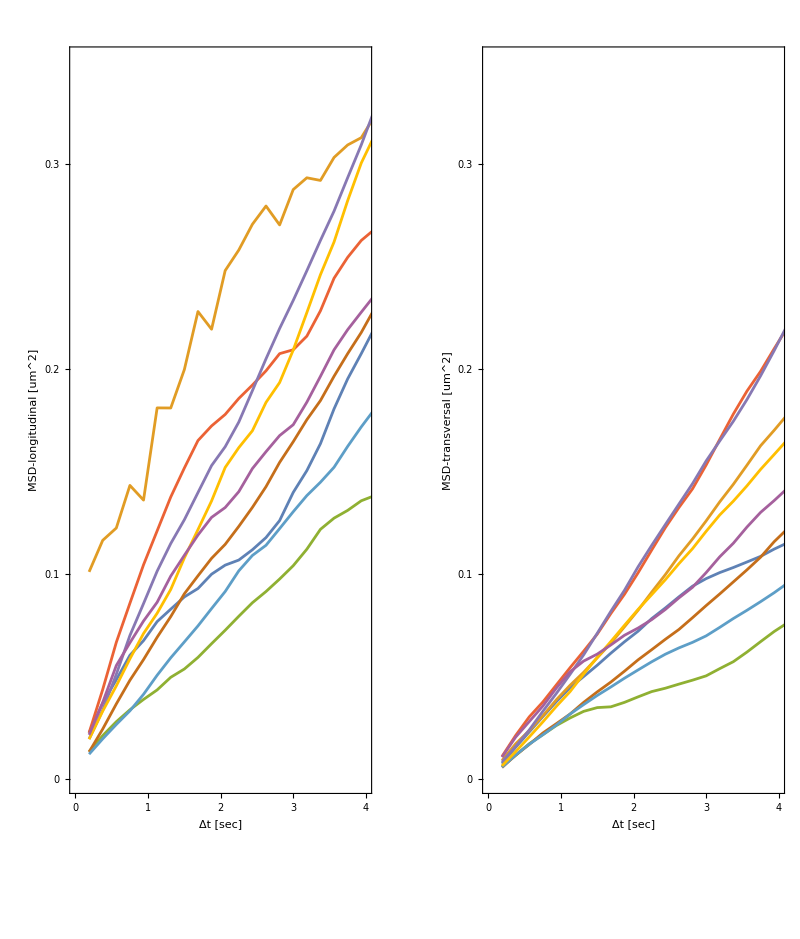

lag time [sec].pdf

```mathematica
verticalPlot=Function[{data,file,n},ListLinePlot[Table[data[[i,All,{1,n}]],{i,Length[file]}],
PlotStyle->Table[{Thickness[0.005],Opacity[1]},{i,Length[file]}],
AspectRatio->1.5 GoldenRatio,
PlotRange->{{0,4},{0,0.35}},
FrameLabel->{{yaxis[[n]],None},{"Δt [sec]",None}},
FrameTicks->{{{0,0.1,0.2,0.3},None},{Range[0,4,1],None}},
Frame->True]];
GraphicsGrid[{{verticalPlot[data90,file90,2],verticalPlot[data90,file90,3]}}]
Export[ToString[yaxis[[1]]]<>".pdf",%]
```